```mathematica
Clear[M,m,R,r,γ,g,J]

M=0.3091; (* mass of tube *)
Ro=0.1985/2; (* outer radius tube *)
Ri=0.1895/2;(* inner radius tube *)
m=0.240; (* extra mass *)
d=0.014; (* diameter extra mass *)
r=Ri-d/2; (* position extra mass *)
γ=m/(M+m); (* relative position centre of mass *)
g=9.81; (* gravitational acceleration *)

JM=M((Ro^2+Ri^2)/2+(γ r)^2); (* moment of inertia for tube *)
Jm=m ((1-γ)r)^2; (* moment of inertia for extra mass *)

J=JM+Jm; (* total moment of inertia *)


X[t_]:=Ro ϕ[t] (* horizontal position *)

FR[t_]:=(m+M)(X''[t]-γ r D[Sin[ϕ[t]],{t,2}]) (* friction *)
FN[t_]:=(m+M)(-γ r D[Cos[ϕ[t]],{t,2}]+g) (* normal force *)

de:=J*ϕ''[t]==-FR[t](Ro-γ r Cos[ϕ[t]])-FN[t] γ r Sin[ϕ[t]] (* differential equation *)
```

```mathematica
data1=Import[FileNameJoin[{NotebookDirectory[],"Data","Large Oscillation 1.csv"}]];
data2=Import[FileNameJoin[{NotebookDirectory[],"Data","Large Oscillation 2.csv"}]];
data3=Import[FileNameJoin[{NotebookDirectory[],"Data","Large Oscillation 3.csv"}]];
data4=Import[FileNameJoin[{NotebookDirectory[],"Data","Large Oscillation 4.csv"}]];

n=4;
```

```mathematica
time={Table[data1[[i,1]],{i,1,Length[data1]}],Table[data2[[i,1]],{i,1,Length[data2]}],Table[data3[[i,1]],{i,1,Length[data3]}],Table[data4[[i,1]],{i,1,Length[data4]}]};

position={Table[data1[[i,2]]/1000,{i,1,Length[data1]}],Table[data2[[i,2]]/1000,{i,1,Length[data2]}],Table[data3[[i,2]]/1000,{i,1,Length[data3]}],Table[data4[[i,2]]/1000,{i,1,Length[data4]}]};

speed={Table[data1[[i,3]]/1000,{i,1,Length[data1]}],Table[data2[[i,3]]/1000,{i,1,Length[data2]}],Table[data3[[i,3]]/1000,{i,1,Length[data3]}],Table[data4[[i,3]]/1000,{i,1,Length[data4]}]};

Φi=Table[Max[position[[i]]]/Ro,{i,1,n}]; (* amplitudes *)
ti=Table[time[[i,Position[position[[i]],Max[position[[i]]]][[1,1]]]],{i,1,n}]; (* time of first turning point *)

tmin=Table[time[[i,1]],{i,1,n}];(* start time *)
tmax=Table[time[[i,Length[time[[i]]]]],{i,1,n}]; (* end time *)
```

```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Times New Roman",FontSize->9}];
SetOptions[ParametricPlot,BaseStyle->{FontFamily->"Times New Roman",FoFontSize->9}];
al={Black,FontSize->11};
```

```mathematica
sol=Table[NDSolve[{de,ϕ[ti[[i]]]==Φi[[i]],ϕ'[ti[[i]]]==0},ϕ,{t,tmin[[i]],tmax[[i]]}] ,{i,1,n}];(* numerical solution *)
```

```mathematica
Needs["ErrorBarPlots`"]
Table[Show[{Plot[Evaluate[X[t]/.sol[[i]]],{t,tmin[[i]],tmax[[i]]},PlotStyle->Blue],ErrorListPlot[Table[{{time[[i,j]],position[[i,j]]},ErrorBar[0.002]},{j,1,Length[time[[i]]]}],PlotStyle->Red]},Frame->True,FrameLabel->{Style["Time (s)",al],Style["Horizontal Position (m)",al]},ImageSize->{350 GoldenRatio,350}],{i,1,n}];
(* X vs t *)
```

```mathematica
length={32,33,34,35};
Table[Show[{ParametricPlot[Evaluate[{X[t],X'[t]}/.sol[[i]]],{t,tmin[[i]],tmax[[i]]}, AspectRatio->1,PlotStyle->{Thick,Blue}],ListPlot[Table[{position[[i,j]],speed[[i,j]]},{j,1,length[[i]]}],PlotStyle->Red]},Frame->True,FrameLabel->{Style["X (m)",al],Style["V (m/s)",al]},ImageSize->{350 GoldenRatio,350}],{i,1,n}];
(* phase space *)
```

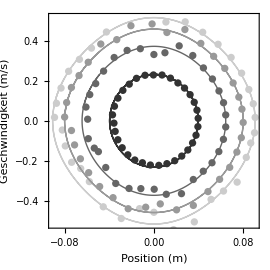

```mathematica
color=Table[GrayLevel[0.2 i],{i,1,4}];
style={Dashed,Dotted,DotDashed,Dashed};
Show[Table[{ParametricPlot[Evaluate[{X[t],X'[t]}/.sol[[i]]],{t,tmin[[i]],tmax[[i]]}, AspectRatio->1,PlotStyle->{Thick,color[[i]]}],ListPlot[Table[{position[[i,j]],speed[[i,j]]},{j,1,length[[i]]}],PlotStyle->color[[i]]]},{i,n,1,-1}],Frame->True,FrameLabel->{Style["Position (m)",al],Style["Geschwindigkeit (m/s)",al]},ImageSize->{270,270}]
```